```mathematica
∫xⅆx
```

x^2/2

```mathematica
Integrate[x,x]
```

x^2/2

```mathematica
∫(x+x^3) ⅆx
```

x^2/2+x^4/4

```mathematica
∫ⅆx/(x^2+3)
```

ArcTan[x/(√3)]/(√3)

```mathematica
Integrate[x/(x^2+x-2),x]
```

1/3 Log[-1+x]+2/3 Log[2+x]

```mathematica
Integrate[x*Cos[x], x]
```

Cos[x]+x Sin[x]

```mathematica
Integrate[x^2*ⅇ^-x, x]
```

ⅇ^-x (-2-2 x-x^2)

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π Erf[x]

```mathematica
∫Sin[x^2] ⅆx
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
∫(x^3-6 x+3)ⅆx
```

3 x-3 x^2+x^4/4

```mathematica
∫1/(7 x^2) ⅆx
```

-1/(7 x)

```mathematica
∫5 √x ⅆx
```

(10 x^(3/2))/3

```mathematica
∫((Cos[x])-Sin[x])ⅆx
```

Cos[x]+Sin[x]

```mathematica
∫(t^2 Sin[t]) ⅆt
```

-(-2+t^2) Cos[t]+2 t Sin[t]

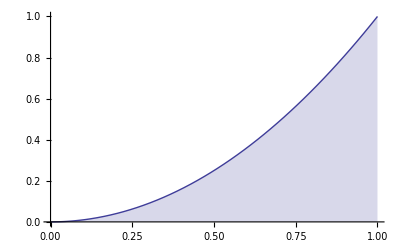

```mathematica
Plot[x^2,{x,0,1},Filling->Axis]
```

```mathematica
Floor[x] -The biggest integer less or equal to x
```

-biggest equal integer less or The to x+Floor[x]

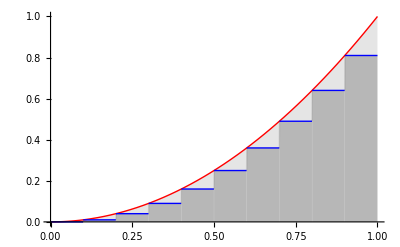

```mathematica
Plot[{x^2,(Floor[10 x]/10)^2},{x,0,1},PlotStyle -> {Red,Blue},Filling->{1->{Axis,Opacity[0.1]},2->{Axis,Opacity[0.2]}}]
```

```mathematica
∑_(i=1)^10 ((i-1)/10)^2*1/10 //N
```

0.285

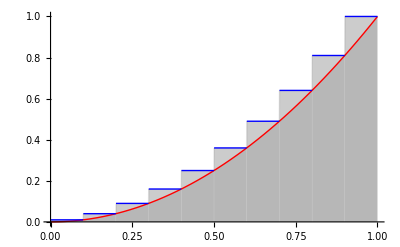

```mathematica
Plot[{x^2,(Floor[10 x+1]/10)^2},{x,0,1},PlotStyle -> {Red,Blue},Filling->{1->{Axis,Opacity[0.1]},2->{Axis,Opacity[0.2]}}]
```

```mathematica
∑_(i=1)^10 (i/10)^2*1/10 //N
```

0.385

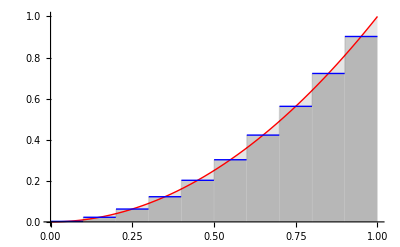

```mathematica
Plot[{x^2,((Floor[10 x]+0.5)/10)^2},{x,0,1},PlotStyle -> {Red,Blue},Filling->{1->{Axis,Opacity[0.1]},2->{Axis,Opacity[0.2]}}]
```

```mathematica
∑_(i=1)^10 ((i-0.5)/10)^2*1/10 //N
```

0.3325

```mathematica
areaR[n_]:=∑_(i=1)^n (i/n)^2*1/n
```

```mathematica
Table[areaR[n]//N,{n,10,100,10}]
```

{0.385,0.35875,0.350185,0.345938,0.3434,0.341713,0.34051,0.339609,0.338909,0.33835}

```mathematica
areaR[n]
```

((1+n) (1+2 n))/(6 n^2)

```mathematica
Limit[areaR[n],n->Infinity]
```

1/3

```mathematica
F[x_] := x^3-5*x^2+8*x-4
```

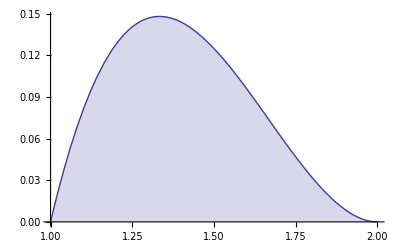

```mathematica
Plot[F[x],{x,1,2},Filling->Axis]
```

```mathematica
areaR[n_] :=∑_(i=1)^n (F[1+i*1/n])*1/n
```

```mathematica
Table[areaR[n]//N,{n,10,100,30}] // TableForm
```

0.0825
0.0832813
0.0833163
0.083325

```mathematica
areaR[n] // Simplify
```

(-1+n^2)/(12 n^2)

```mathematica
Limit[areaR[n],n->Infinity]
```

1/12

```mathematica
F[x_] := Sin[x]
```

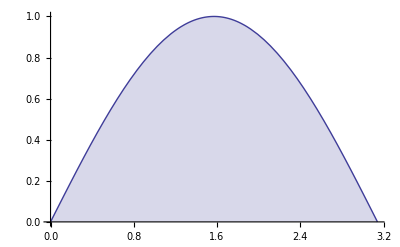

```mathematica
Plot[F[x],{x,0,π},Filling->Axis]
```

```mathematica
areaR[n_] := ∑_(i=1)^n (F[0+(i*π)/n])*π/n
```

```mathematica
Table[areaR[n]//N,{n,10,100,10}] //TableForm
```

1.98352
1.99589
1.99817
1.99897
1.99934
1.99954
1.99966
1.99974
1.9998
1.99984

```mathematica
Limit[arreaR[n],{n->Infinity}]
```

{Limit[arreaR[n],n→∞]}

```mathematica
f[x_] := 2-x^2
```

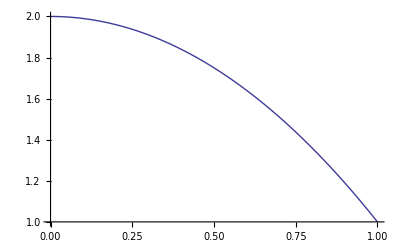

```mathematica
Plot[f[x],{x,0,1}]
```

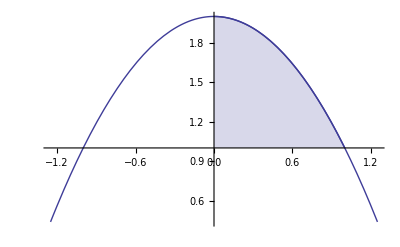

```mathematica
Show[Plot[f[x],{x,0,1},Filling->Axis],Plot[f[x],{x,-1.25,1.25}],PlotRange->All]
```

```mathematica
IntApprox[n_] := ∑_(i=1)^n f[i/n]*1/n
```

```mathematica
IntApprox[100] //N
```

1.66165

```mathematica
IntApprox[x] //Simplify
```

-(1+3 x-10 x^2)/(6 x^2)

```mathematica
Limit[IntApprox[n],n->Infinity]
```

5/3

```mathematica
Clear[f,x]
```

```mathematica
f[x_] := x^3-1
```

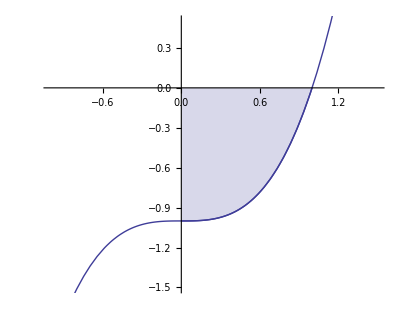

```mathematica
Show[Plot[f[x],{x,0,1}, Filling->Axis],Plot[f[x],{x,-1,1.5}],PlotRange->{{-1,1.5},{-1.5,.5}},AspectRatio->Automatic]
```

```mathematica
a=0;
```

```mathematica
b=1;
```

```mathematica
intApprox[n_] := ∑_(i=1)^n f[a+(i*(b-a))/n]*(b-a)/n
```

```mathematica
intApprox[100] //N
```

-0.744975

```mathematica
intApprox[n] //Simplify
```

-((-1+n) (1+3 n))/(4 n^2)

```mathematica
Limit[intApprox[n],n->Infinity]
```

-3/4

```mathematica
Clear[f,x,intApprox, a, b]
```

```mathematica
f[x_] := x^2-1
```

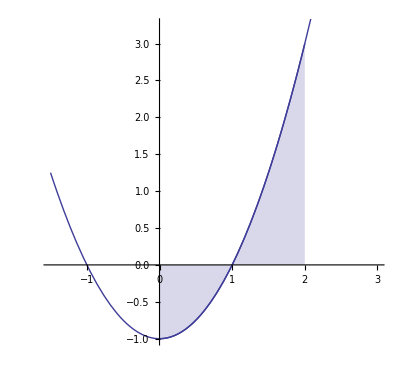

```mathematica
Show[Plot[f[x],{x,0,2}, Filling->Axis],Plot[f[x],{x,-1.5,3}],PlotRange->{{-1.5,3},{-1,3.25}},AspectRatio->Automatic]
```

```mathematica
a=0;
```

```mathematica
b=2;
```

```mathematica
intApprox[n_] := ∑_(i=1)^n f[a+(i*(b-a))/n]*(b-a)/n
```

```mathematica
intApprox[100] //N
```

0.7068

```mathematica
intApprox[n] //Simplify
```

(2 (2+6 n+n^2))/(3 n^2)

```mathematica
Limit[intApprox[n],n->Infinity]
```

2/3

```mathematica
Clear[a,b]
```

```mathematica
a=0;
```

```mathematica
b=1;
```

```mathematica
intApprox[n_]:=area1=-Limit[intApprox[n],n->Infinity]
```

```mathematica
a=1;
```

```mathematica
b=2;
```

```mathematica
intApprox[n_]:=area2= Limit[intApprox[n],n->Infinity]
```

```mathematica
area1+area2
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

```mathematica
integralMovie[func_,{x_,a_,b_},{ymin_,ymax_},sumRule_] :=Module[{apprx,f,stepfn,nrects,dx,plot},f[t_]=func  /.x->t; stepfn[t_,n_]=f[a+(Ceiling[n*(t-a)/(b-a)]-sumRule)(b-a)/n] ; Animate[dx=N[(b-a)/2^k]; approx=Sum[f[a+(i-sumRule)dx], {i,1,2^k}]; Show[Plot[{f[x],stepfn[x,2^k]},{x,a,b},PlotPoints->200,PlotStyle->{{Red},{Black}},Filling->Axis,PlotRange->{ymin,ymax},PlotLabel->{2^k,apprx}]],{k,1,8,1}]]
```

```mathematica
integralMovie[x^18-36*x^16+9*x^8,{x,0,4},{0,13},.5]
```

```mathematica
f[x_] := x
a:=0
```

```mathematica
F[x_] := Limit[∑_(i=1)^n f[a+(i*(x-a))/n]*(x-a)/n, n->Infinity]
```

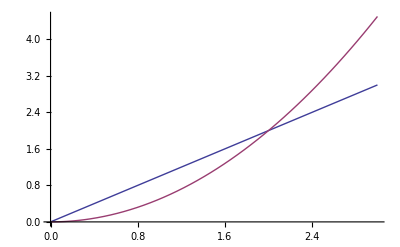

```mathematica
Plot[{f[x],F[x]},{x,0,3}]
```

```mathematica
Table[{x,F[x]},{x,0,4}] // TableForm
```

0 | 0
1 | 1/2
2 | 2
3 | 9/2
4 | 8

```mathematica
F[x]
```

x^2/2

```mathematica
Clear[f,F,a]
```

```mathematica
f[x_] := 2*x-x^2
a:=0
```

```mathematica
F[x_] :=Limit[∑_(i=1)^n f[a+(i*(x-a))/n]*(x-a)/n, n->Infinity]
```

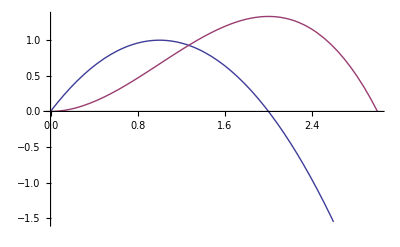

```mathematica
Plot[{f[x],F[x]},{x,0,3}]
```

```mathematica
F[x]
```

-1/3 (-3+x) x^2

```mathematica
Integrate[1/(x^2+1),{x,1,3}] 
%// N
```

-π/4+ArcTan[3]

0.463648

```mathematica
Integrate[Sin[3*x]*Cos[2*x],{x,0,π}]
```

6/5

```mathematica
Assuming[x>0,Integrate[1/t^2,{t,1,x}]]
```

(-1+x)/x

```mathematica
∫Sin[x^2] ⅆx
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π Erf[x]

```mathematica
FresnelS[1] //N
```

0.438259

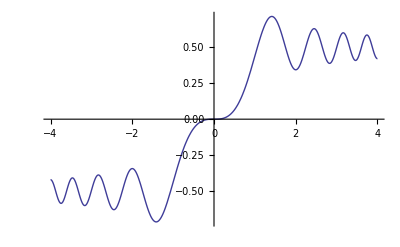

```mathematica
Plot[FresnelS[x],{x,-4,4}]
```

```mathematica
Assuming[t>1,Integrate[x^(-3/2),{x,1,t}]]
```

2-2/(√t)

```mathematica
Limit[%,t->Infinity]
```

2

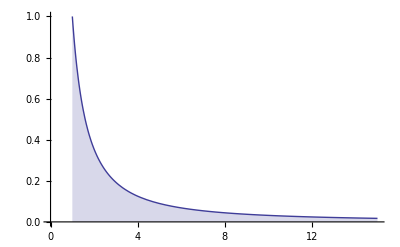

```mathematica
Plot[x^(-3/2),{x,1,15}, PlotRange->{{0,15},All},Filling->Axis]
```

```mathematica
∫_0^1 1/(√(ⅇ^x-1))ⅆx - несобствен интеграл от 2-ри тип(подинт. ф-я има вертикална асимптота в долната граница 0)
```

2 ArcTan[√(-1+ⅇ)]

```mathematica
Assuming[0<t<1, ∫_t^1 1/(√(ⅇ^x-1))ⅆx]
```

2 (ArcTan[√(-1+ⅇ)]-ArcTan[√(-1+ⅇ^t)])

```mathematica
Limit[%,t->0,Direction->-1]
```

2 ArcTan[√(-1+ⅇ)]

```mathematica
%//N
```

1.83821

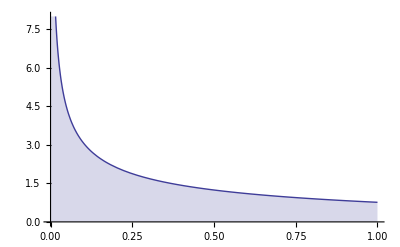

```mathematica
Plot[1/(√(ⅇ^x-1)),{x,0,1},PlotRange->{0,8},Filling->Axis]
```

```mathematica
∫_0^(π/2) Tan[x]ⅆx
```

Integrate::idiv: Integral of Tan[x] does not converge on {0, π/2}.

∫_0^(π/2) Tan[x]ⅆx

```mathematica
Assuming[0<t<π/2,∫_0^t Tan[x]ⅆx]
```

-Log[Cos[t]]

```mathematica
Limit[%,t->π/2]
```

∞

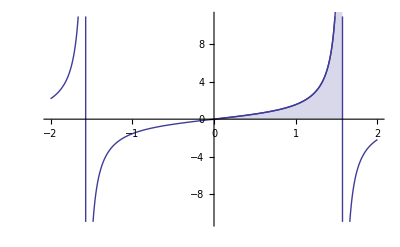

```mathematica
Show[Plot[Tan[x],{x,-2,2}],Plot[Tan[x],{x,0,π/2},Filling->Axis,PlotRange->{-12,12}]]
```

```mathematica
∫_0^1 1/(√x*(1-√x))ⅆx
```

Integrate::idiv: Integral of 1/√x - x does not converge on {0, 1}.

∫_0^1 1/((1-√x) √x)ⅆx

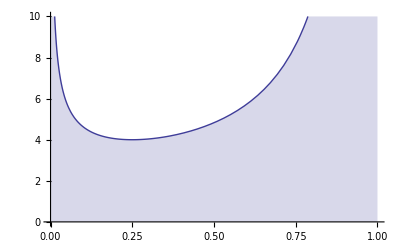

```mathematica
Plot[1/(√x*(1-√x)),{x,0,1},PlotRange->{0,10},Filling->Axis]
```

```mathematica
∫1/(√x*(1-√x))ⅆx
```

-2 Log[-1+√x]

```mathematica
Limit[%,x->1,Direction->1]-Limit[%,x->0,Direction->-1]
```

0

```mathematica
Limit[%,x->1,Direction->1]
```

0

```mathematica
Limit[%,x->0,Direction->-1]
```

0